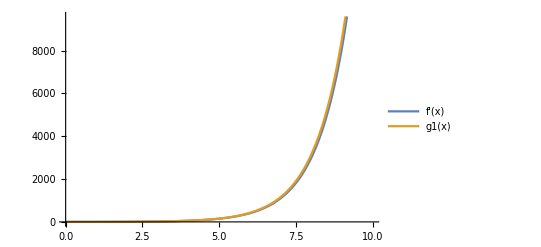

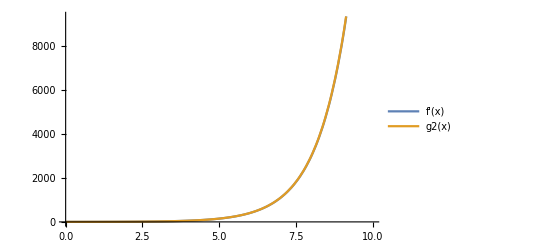

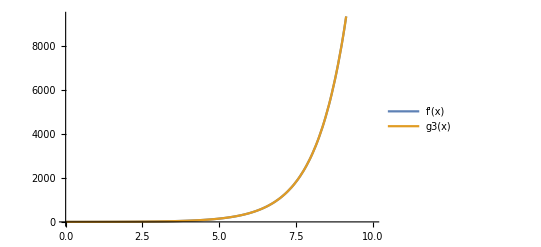

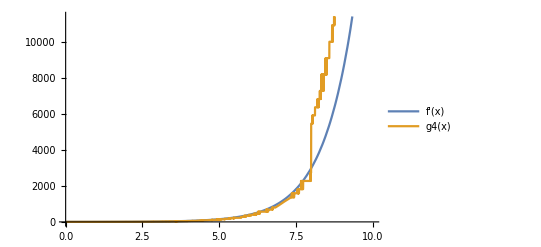

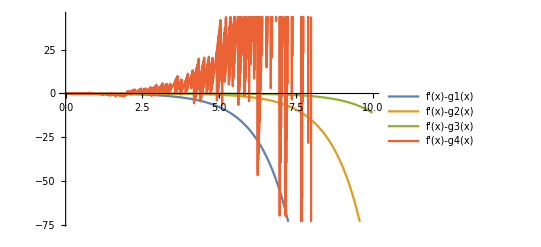

```mathematica
f[t_]=Exp[t];
h1=0.1;
h2=0.01;
h3=0.001;
h4=10^(-15);
g1[t_]=(f[t+h1]-f[t])/h1;
g2[t_]=(f[t+h2]-f[t])/h2;
g3[t_]=(f[t+h3]-f[t])/h3;
g4[t_]=(f[t+h4]-f[t])/h4;
Plot[{f'[x],g1[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g2[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g3[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g4[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{(f'[x]-g1[x]),(f'[x]-g2[x]),(f'[x]-g3[x]),(f'[x]-g4[x])},{x,0,10},PlotLegends->"Expressions"]
```

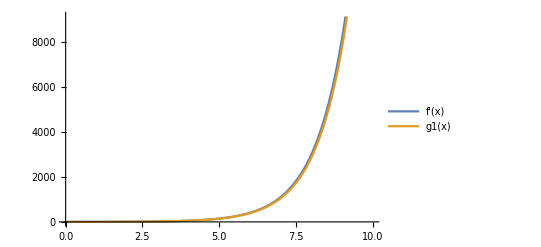

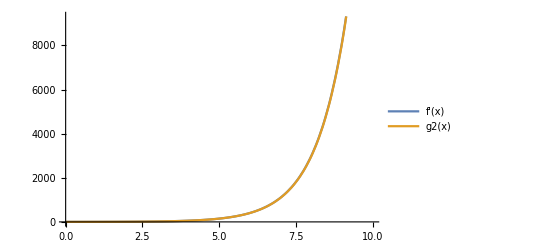

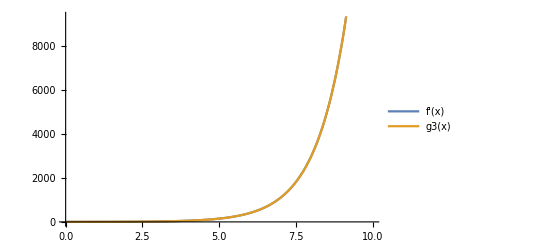

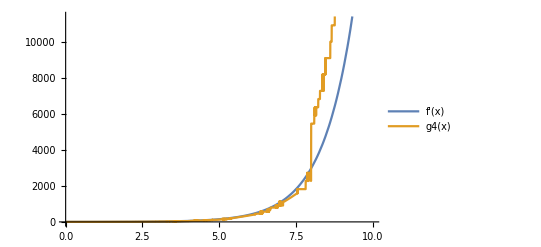

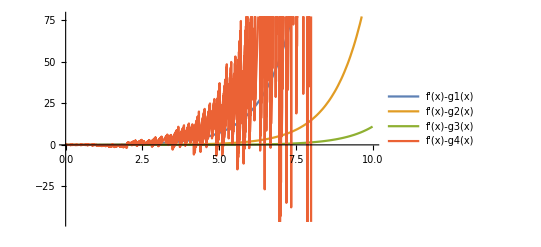

```mathematica
f[t_]=Exp[t];
h1=0.1;
h2=0.01;
h3=0.001;
h4=0.1^15;
g1[t_]=(f[t]-f[t-h1])/h1;
g2[t_]=(f[t]-f[t-h2])/h2;
g3[t_]=(f[t]-f[t-h3])/h3;
g4[t_]=(f[t]-f[t-h4])/h4;
Plot[{f'[x],g1[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g2[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g3[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g4[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{(f'[x]-g1[x]),(f'[x]-g2[x]),(f'[x]-g3[x]),(f'[x]-g4[x])},{x,0,10},PlotLegends->"Expressions"]
```

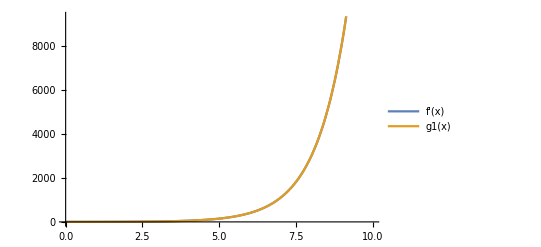

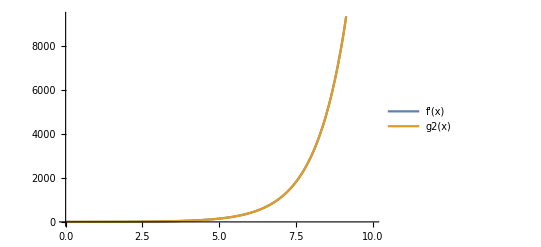

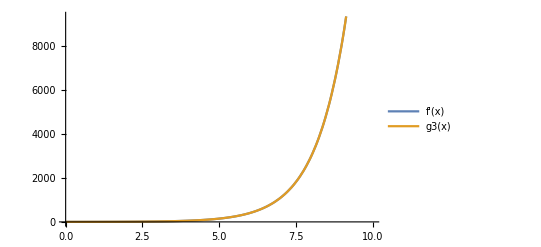

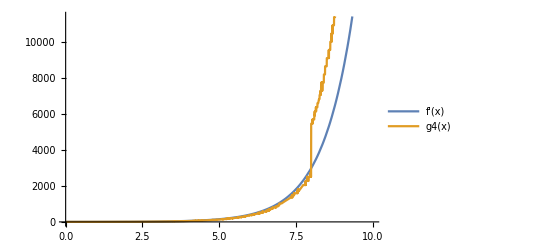

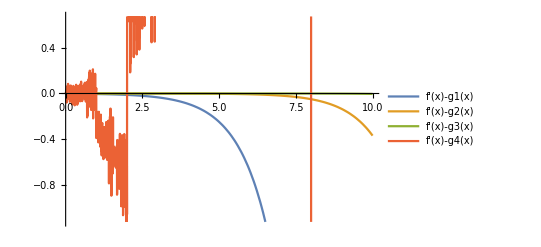

```mathematica
f[t_]=Exp[t];
h1=0.1;
h2=0.01;
h3=0.001;
h4=0.1^15;
g1[t_]=(f[t+h1]-f[t-h1])/(2*h1);
g2[t_]=(f[t+h2]-f[t-h2])/(2*h2);
g3[t_]=(f[t+h3]-f[t-h3])/(2*h3);
g4[t_]=(f[t+h4]-f[t-h4])/(2*h4);
Plot[{f'[x],g1[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g2[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g3[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f'[x],g4[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{(f'[x]-g1[x]),(f'[x]-g2[x]),(f'[x]-g3[x]),(f'[x]-g4[x])},{x,0,10},PlotLegends->"Expressions"]
```

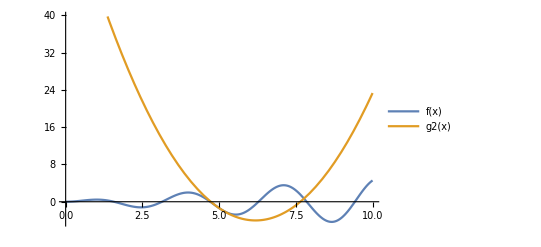

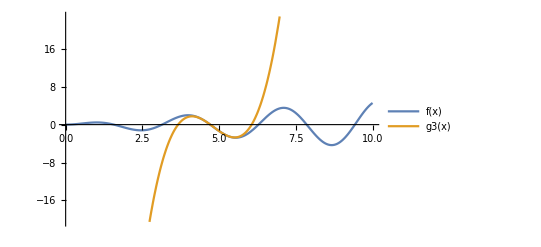

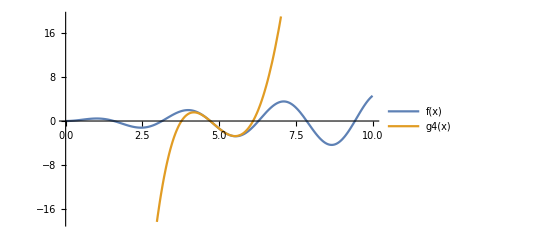

Set::write: Tag Times in (x Cos[x] Sin[x])[t_] is Protected.

```mathematica
f[t_]=t*Sin[t]*Cos[t];
g2[t_]=Normal[Series[f[t],{t,5,2}]];
g3[t_]=Normal[Series[f[t],{t,5,3}]];
g4[t_]=Normal[Series[f[t],{t,5,4}]];
Plot[{f[x],g2[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f[x],g3[x]},{x,0,10},PlotLegends->"Expressions"]
Plot[{f[x],g4[x]},{x,0,10},PlotLegends->"Expressions"]
n=5;
gn[t_]=Normal[Series[f[t],{t,a,n}]];
(*Manipulate[Plot[{f[x],Normal[Series[f[x],{x,a,n}]]},{x,0,10}],{a,0,10},{n,1,10}]*)
Manipulate[Plot[{f[x],gn[x]},{x,0,10}],{a,0,10}]
```

```mathematica
Normal[Series[f[x],{x,a,n}]]
Normal[Series[f[t_],{t,a,n}]]
```

a Cos[a] Sin[a]+(-a+x)^2 (Cos[a]^2-2 a Cos[a] Sin[a]-Sin[a]^2)+2/3 (-a+x)^4 (-Cos[a]^2+a Cos[a] Sin[a]+Sin[a]^2)-2/3 (-a+x)^3 (a Cos[a]^2+3 Cos[a] Sin[a]-a Sin[a]^2)+2/15 (-a+x)^5 (a Cos[a]^2+5 Cos[a] Sin[a]-a Sin[a]^2)+(-a+x) (a Cos[a]^2+Sin[a] (Cos[a]-a Sin[a]))

Cos[a_] a_ Sin[a_]+(-a+t) (Cos[a_]^2 a_ Pattern^(1,0)[a,_]+Sin[a_] (Cos[a_] Pattern^(1,0)[a,_]-a_ Sin[a_] Pattern^(1,0)[a,_]))+1/2 (-a+t)^2 (2 Cos[a_]^2 (Pattern^(1,0)[a,_])^2-4 Cos[a_] a_ Sin[a_] (Pattern^(1,0)[a,_])^2-2 Sin[a_]^2 (Pattern^(1,0)[a,_])^2+Cos[a_]^2 a_ Pattern^(2,0)[a,_]+Cos[a_] Sin[a_] Pattern^(2,0)[a,_]-a_ Sin[a_]^2 Pattern^(2,0)[a,_])+1/6 (-a+t)^3 (-4 Cos[a_]^2 a_ (Pattern^(1,0)[a,_])^3-12 Cos[a_] Sin[a_] (Pattern^(1,0)[a,_])^3+4 a_ Sin[a_]^2 (Pattern^(1,0)[a,_])^3+6 Cos[a_]^2 Pattern^(1,0)[a,_] Pattern^(2,0)[a,_]-12 Cos[a_] a_ Sin[a_] Pattern^(1,0)[a,_] Pattern^(2,0)[a,_]-6 Sin[a_]^2 Pattern^(1,0)[a,_] Pattern^(2,0)[a,_]+Cos[a_]^2 a_ Pattern^(3,0)[a,_]+Cos[a_] Sin[a_] Pattern^(3,0)[a,_]-a_ Sin[a_]^2 Pattern^(3,0)[a,_])+1/24 (-a+t)^4 (-16 Cos[a_]^2 (Pattern^(1,0)[a,_])^4+16 Cos[a_] a_ Sin[a_] (Pattern^(1,0)[a,_])^4+16 Sin[a_]^2 (Pattern^(1,0)[a,_])^4-24 Cos[a_]^2 a_ (Pattern^(1,0)[a,_])^2 Pattern^(2,0)[a,_]-72 Cos[a_] Sin[a_] (Pattern^(1,0)[a,_])^2 Pattern^(2,0)[a,_]+24 a_ Sin[a_]^2 (Pattern^(1,0)[a,_])^2 Pattern^(2,0)[a,_]+6 Cos[a_]^2 (Pattern^(2,0)[a,_])^2-12 Cos[a_] a_ Sin[a_] (Pattern^(2,0)[a,_])^2-6 Sin[a_]^2 (Pattern^(2,0)[a,_])^2+8 Cos[a_]^2 Pattern^(1,0)[a,_] Pattern^(3,0)[a,_]-16 Cos[a_] a_ Sin[a_] Pattern^(1,0)[a,_] Pattern^(3,0)[a,_]-8 Sin[a_]^2 Pattern^(1,0)[a,_] Pattern^(3,0)[a,_]+Cos[a_]^2 a_ Pattern^(4,0)[a,_]+Cos[a_] Sin[a_] Pattern^(4,0)[a,_]-a_ Sin[a_]^2 Pattern^(4,0)[a,_])+1/120 (-a+t)^5 (16 Cos[a_]^2 a_ (Pattern^(1,0)[a,_])^5+80 Cos[a_] Sin[a_] (Pattern^(1,0)[a,_])^5-16 a_ Sin[a_]^2 (Pattern^(1,0)[a,_])^5-160 Cos[a_]^2 (Pattern^(1,0)[a,_])^3 Pattern^(2,0)[a,_]+160 Cos[a_] a_ Sin[a_] (Pattern^(1,0)[a,_])^3 Pattern^(2,0)[a,_]+160 Sin[a_]^2 (Pattern^(1,0)[a,_])^3 Pattern^(2,0)[a,_]-60 Cos[a_]^2 a_ Pattern^(1,0)[a,_] (Pattern^(2,0)[a,_])^2-180 Cos[a_] Sin[a_] Pattern^(1,0)[a,_] (Pattern^(2,0)[a,_])^2+60 a_ Sin[a_]^2 Pattern^(1,0)[a,_] (Pattern^(2,0)[a,_])^2-40 Cos[a_]^2 a_ (Pattern^(1,0)[a,_])^2 Pattern^(3,0)[a,_]-120 Cos[a_] Sin[a_] (Pattern^(1,0)[a,_])^2 Pattern^(3,0)[a,_]+40 a_ Sin[a_]^2 (Pattern^(1,0)[a,_])^2 Pattern^(3,0)[a,_]+20 Cos[a_]^2 Pattern^(2,0)[a,_] Pattern^(3,0)[a,_]-40 Cos[a_] a_ Sin[a_] Pattern^(2,0)[a,_] Pattern^(3,0)[a,_]-20 Sin[a_]^2 Pattern^(2,0)[a,_] Pattern^(3,0)[a,_]+10 Cos[a_]^2 Pattern^(1,0)[a,_] Pattern^(4,0)[a,_]-20 Cos[a_] a_ Sin[a_] Pattern^(1,0)[a,_] Pattern^(4,0)[a,_]-10 Sin[a_]^2 Pattern^(1,0)[a,_] Pattern^(4,0)[a,_]+Cos[a_]^2 a_ Pattern^(5,0)[a,_]+Cos[a_] Sin[a_] Pattern^(5,0)[a,_]-a_ Sin[a_]^2 Pattern^(5,0)[a,_])

```mathematica
Series[f[t],{t,5,2}]
```

5 Cos[5] Sin[5]+(5 Cos[5]^2+(Cos[5]-5 Sin[5]) Sin[5]) (t-5)+(Cos[5]^2-10 Cos[5] Sin[5]-Sin[5]^2) (t-5)^2+O[t-5]^3

```mathematica
(*f[t_]=Exp[t];*)
g2[t_]=Series[f[t],{t,5,2}];
g2[t]-f'[t]
```

(-ⅇ^5+5 Cos[5] Sin[5])+(-ⅇ^5+5 Cos[5]^2+(Cos[5]-5 Sin[5]) Sin[5]) (t-5)+(-ⅇ^5/2+Cos[5]^2-10 Cos[5] Sin[5]-Sin[5]^2) (t-5)^2+O[t-5]^3